-Graphics3D-

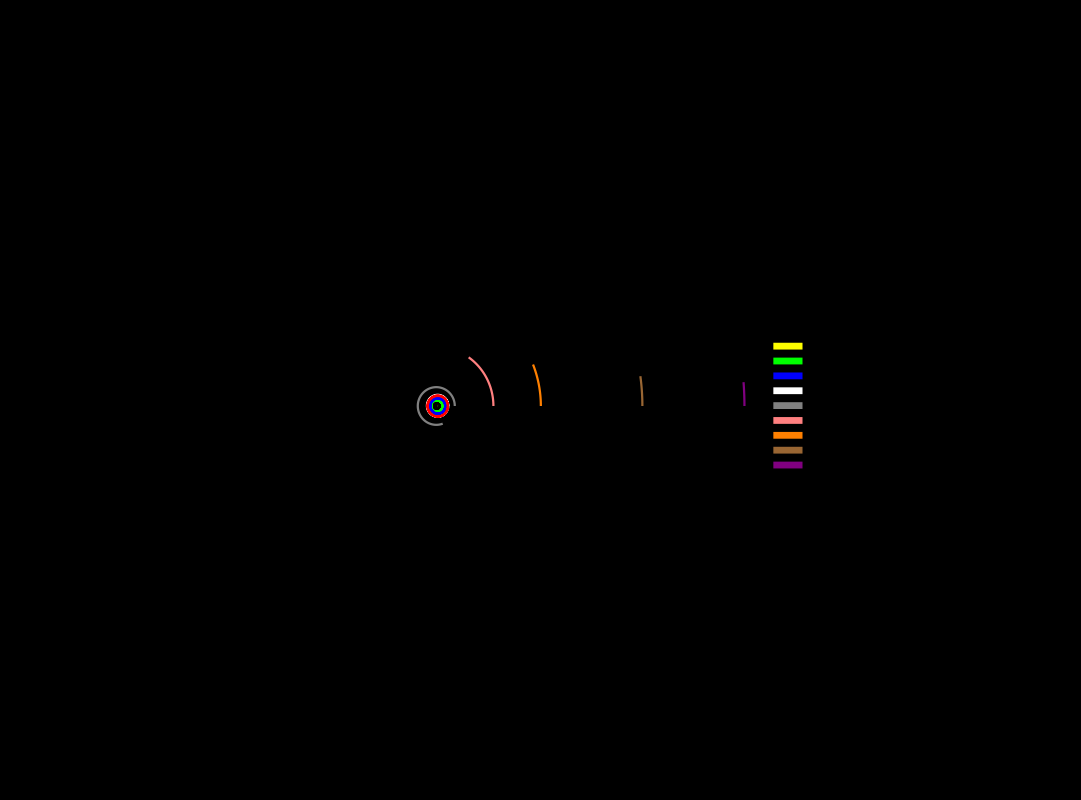

-Graphics-

-Graphics-

```mathematica
(*SIMULAÇÃO DE CORPO NO SISTEMA SOLAR COM VISUALIZAÇÃO TRIDIMENSIONAL*)

(*PARÂMETROS DO CORPO DE TESTE*)
m10=6*10^24;

x10o=1.5*10^11;
y10o=0;
z10o=0;

vx10o=0;
vy10o=29871;
vz10o=0;







(*Parâmetros de Definição*)
ms=2*10^30;
rs=696340000;
ua=1.5*10^11;
ano=60*60*24*365;
graus=Pi/180;
u=6.67*10^-11;

(*Configurações Gerais da Simulação*)
temp=Evaluate[Input["Escreva o tempo decorrido em anos."]];
tempo=temp*ano;
escv=4503443661000;
escp=1;

(*Parâmetros dos Oito Corpos do Sistem Solar*)
r1=rs;
r2=rs;
r3=rs;
r4=rs;
r5=rs;
r6=rs;
r7=rs;
r8=rs;
r9=rs;
r10=rs;

m1=2*10^30;
m2=3.3*10^23;
m3=4.9*10^24;
m4=6*10^24;
m5=6.4*10^24;
m6=1.9*10^27;
m7=5.7*10^26;
m8=8.7*10^25;
m9=1*10^26;

x1o=0;
x2o=69816900000;
x3o=108942000000;
x4o=152098232000;
x5o=249209300000;
x6o=816520800000;
x7o=1513325783000;
x8o=3004419704000;
x9o=4503443661000;
y1o=0;
y2o=0;
y3o=0;
y4o=0;
y5o=0;
y6o=0;
y7o=0;
y8o=0;
y9o=0;
z1o=0;
z2o=0;
z3o=0;
z4o=0;
z5o=0;
z6o=0;
z7o=0;
z8o=0;
z9o=0;

vx1o=0;
vx2o=0;
vx3o=0;
vx4o=0;
vx5o=0;
vx6o=0;
vx7o=0;
vx8o=0;
vx9o=0;
vy1o=0;
vy2o=47362;
vy3o=35020;
vy4o=29780;
vy5o=24077;
vy6o=13070;
vy7o=9690;
vy8o=6810;
vy9o=5430;
vz1o=0;
vz2o=0;
vz3o=0;
vz4o=0;
vz5o=0;
vz6o=0;
vz7o=0;
vz8o=0;
vz9o=0;

(*Corpo da Simulação*)
trajetoria=NDSolve[{x1''[t]==u*((m2*(x2[t]-x1[t]))/(Sqrt[(x1[t]-x2[t])^2+(y1[t]-y2[t])^2+(z1[t]-z2[t])^2]^3)+(m3*(x3[t]-x1[t]))/(Sqrt[(x1[t]-x3[t])^2+(y1[t]-y3[t])^2+(z1[t]-z3[t])^2]^3)+(m4*(x4[t]-x1[t]))/(Sqrt[(x1[t]-x4[t])^2+(y1[t]-y3[t])^2+(z1[t]-z4[t])^2]^3)+(m5*(x5[t]-x1[t]))/(Sqrt[(x1[t]-x5[t])^2+(y1[t]-y5[t])^2+(z1[t]-z5[t])^2]^3)+(m6*(x6[t]-x1[t]))/(Sqrt[(x1[t]-x6[t])^2+(y1[t]-y6[t])^2+(z1[t]-z6[t])^2]^3)+(m7*(x7[t]-x1[t]))/(Sqrt[(x1[t]-x7[t])^2+(y1[t]-y7[t])^2+(z1[t]-z7[t])^2]^3)+(m8*(x8[t]-x1[t]))/(Sqrt[(x1[t]-x8[t])^2+(y1[t]-y8[t])^2+(z1[t]-z8[t])^2]^3)+(m9*(x9[t]-x1[t]))/(Sqrt[(x1[t]-x9[t])^2+(y1[t]-y9[t])^2+(z1[t]-z9[t])^2]^3)+(m10*(x10[t]-x1[t]))/(Sqrt[(x1[t]-x10[t])^2+(y1[t]-y10[t])^2+(z1[t]-z10[t])^2]^3)),y1''[t]==u*((m2*(y2[t]-y1[t]))/(Sqrt[(x1[t]-x2[t])^2+(y1[t]-y2[t])^2+(z1[t]-z2[t])^2]^3)+(m3*(y3[t]-y1[t]))/(Sqrt[(x1[t]-x3[t])^2+(y1[t]-y3[t])^2+(z1[t]-z2[t])^2]^3)+(m4*(y4[t]-y1[t]))/(Sqrt[(x1[t]-x4[t])^2+(y1[t]-y3[t])^2+(z1[t]-z4[t])^2]^3)+(m5*(y5[t]-y1[t]))/(Sqrt[(x1[t]-x5[t])^2+(y1[t]-y5[t])^2+(z1[t]-z5[t])^2]^3)+(m6*(y6[t]-y1[t]))/(Sqrt[(x1[t]-x6[t])^2+(y1[t]-y6[t])^2+(z1[t]-z6[t])^2]^3)+(m7*(y7[t]-y1[t]))/(Sqrt[(x1[t]-x7[t])^2+(y1[t]-y7[t])^2+(z1[t]-z7[t])^2]^3)+(m8*(y8[t]-y1[t]))/(Sqrt[(x1[t]-x8[t])^2+(y1[t]-y8[t])^2+(z1[t]-z8[t])^2]^3)+(m9*(y9[t]-y1[t]))/(Sqrt[(x1[t]-x9[t])^2+(y1[t]-y9[t])^2+(z1[t]-z9[t])^2]^3)+(m10*(y10[t]-y1[t]))/(Sqrt[(x1[t]-x10[t])^2+(y1[t]-y10[t])^2+(z1[t]-z10[t])^2]^3)),x2''[t]==u*((m1*(x1[t]-x2[t]))/(Sqrt[(x1[t]-x2[t])^2+(y1[t]-y2[t])^2+(z1[t]-z2[t])^2]^3)+(m3*(x3[t]-x2[t]))/(Sqrt[(x3[t]-x2[t])^2+(y3[t]-y2[t])^2+(z3[t]-z2[t])^2]^3)+(m4*(x4[t]-x2[t]))/(Sqrt[(x4[t]-x2[t])^2+(y4[t]-y2[t])^2+(z4[t]-z2[t])^2]^3)+(m5*(x5[t]-x2[t]))/(Sqrt[(x5[t]-x2[t])^2+(y5[t]-y2[t])^2+(z5[t]-z2[t])^2]^3)+(m6*(x6[t]-x2[t]))/(Sqrt[(x6[t]-x2[t])^2+(y6[t]-y2[t])^2+(z6[t]-z2[t])^2]^3)+(m7*(x7[t]-x2[t]))/(Sqrt[(x7[t]-x2[t])^2+(y7[t]-y2[t])^2+(z7[t]-z2[t])^2]^3)+(m8*(x8[t]-x2[t]))/(Sqrt[(x8[t]-x2[t])^2+(y8[t]-y2[t])^2+(z8[t]-z2[t])^2]^3)+(m9*(x9[t]-x2[t]))/(Sqrt[(x9[t]-x2[t])^2+(y9[t]-y2[t])^2+(z9[t]-z2[t])^2]^3)+(m10*(x10[t]-x2[t]))/(Sqrt[(x10[t]-x2[t])^2+(y10[t]-y2[t])^2+(z10[t]-z2[t])^2]^3)),y2''[t]==u*((m1*(y1[t]-y2[t]))/(Sqrt[(x1[t]-x2[t])^2+(y1[t]-y2[t])^2+(z1[t]-z2[t])^2]^3)+(m3*(y3[t]-y2[t]))/(Sqrt[(x3[t]-x2[t])^2+(y3[t]-y2[t])^2+(z3[t]-z2[t])^2]^3)+(m4*(y4[t]-y2[t]))/(Sqrt[(x4[t]-x2[t])^2+(y4[t]-y2[t])^2+(z4[t]-z2[t])^2]^3)+(m5*(y5[t]-y2[t]))/(Sqrt[(x5[t]-x2[t])^2+(y5[t]-y2[t])^2+(z5[t]-z2[t])^2]^3)+(m6*(y6[t]-y2[t]))/(Sqrt[(x6[t]-x2[t])^2+(y6[t]-y2[t])^2+(z6[t]-z2[t])^2]^3)+(m7*(y7[t]-y2[t]))/(Sqrt[(x7[t]-x2[t])^2+(y7[t]-y2[t])^2+(z7[t]-z2[t])^2]^3)+(m8*(y8[t]-y2[t]))/(Sqrt[(x8[t]-x2[t])^2+(y8[t]-y2[t])^2+(z8[t]-z2[t])^2]^3)+(m9*(y9[t]-y2[t]))/(Sqrt[(x9[t]-x2[t])^2+(y9[t]-y2[t])^2+(z9[t]-z2[t])^2]^3)+(m10*(y10[t]-y2[t]))/(Sqrt[(x10[t]-x2[t])^2+(y10[t]-y2[t])^2+(z10[t]-z2[t])^2]^3)),x3''[t]==u*((m1*(x1[t]-x3[t]))/(Sqrt[(x1[t]-x3[t])^2+(y1[t]-y3[t])^2+(z1[t]-z3[t])^2]^3)+(m2*(x2[t]-x3[t]))/(Sqrt[(x2[t]-x3[t])^2+(y2[t]-y3[t])^2+(z3[t]-z2[t])^2]^3)+(m4*(x4[t]-x3[t]))/(Sqrt[(x4[t]-x3[t])^2+(y4[t]-y3[t])^2+(z3[t]-z4[t])^2]^3)+(m5*(x5[t]-x3[t]))/(Sqrt[(x5[t]-x3[t])^2+(y5[t]-y3[t])^2+(z3[t]-z5[t])^2]^3)+(m6*(x6[t]-x3[t]))/(Sqrt[(x6[t]-x3[t])^2+(y6[t]-y3[t])^2+(z3[t]-z6[t])^2]^3)+(m7*(x7[t]-x3[t]))/(Sqrt[(x7[t]-x3[t])^2+(y7[t]-y3[t])^2+(z3[t]-z7[t])^2]^3)+(m8*(x8[t]-x3[t]))/(Sqrt[(x8[t]-x3[t])^2+(y8[t]-y3[t])^2+(z3[t]-z8[t])^2]^3)+(m9*(x9[t]-x3[t]))/(Sqrt[(x9[t]-x3[t])^2+(y9[t]-y3[t])^2+(z3[t]-z9[t])^2]^3)+(m10*(x10[t]-x3[t]))/(Sqrt[(x10[t]-x3[t])^2+(y10[t]-y3[t])^2+(z3[t]-z10[t])^2]^3)),y3''[t]==u*((m1*(y1[t]-y3[t]))/(Sqrt[(x1[t]-x3[t])^2+(y1[t]-y3[t])^2+(z1[t]-z3[t])^2]^3)+(m2*(y2[t]-y3[t]))/(Sqrt[(x2[t]-x3[t])^2+(y2[t]-y3[t])^2+(z3[t]-z2[t])^2]^3)+(m4*(y4[t]-y3[t]))/(Sqrt[(x4[t]-x3[t])^2+(y4[t]-y3[t])^2+(z3[t]-z4[t])^2]^3)+(m5*(y5[t]-y3[t]))/(Sqrt[(x5[t]-x3[t])^2+(y5[t]-y3[t])^2+(z3[t]-z5[t])^2]^3)+(m6*(y6[t]-y3[t]))/(Sqrt[(x6[t]-x3[t])^2+(y6[t]-y3[t])^2+(z3[t]-z6[t])^2]^3)+(m7*(y7[t]-y3[t]))/(Sqrt[(x7[t]-x3[t])^2+(y7[t]-y3[t])^2+(z3[t]-z7[t])^2]^3)+(m8*(y8[t]-y3[t]))/(Sqrt[(x8[t]-x3[t])^2+(y8[t]-y3[t])^2+(z3[t]-z8[t])^2]^3)+(m9*(y9[t]-y3[t]))/(Sqrt[(x9[t]-x3[t])^2+(y9[t]-y3[t])^2+(z3[t]-z9[t])^2]^3)+(m10*(y10[t]-y3[t]))/(Sqrt[(x10[t]-x3[t])^2+(y10[t]-y3[t])^2+(z3[t]-z10[t])^2]^3)),x4''[t]==u*((m1*(x1[t]-x4[t]))/(Sqrt[(x1[t]-x4[t])^2+(y1[t]-y4[t])^2+(z4[t]-z1[t])^2]^3)+(m2*(x2[t]-x4[t]))/(Sqrt[(x2[t]-x4[t])^2+(y2[t]-y4[t])^2+(z4[t]-z2[t])^2]^3)+(m3*(x3[t]-x4[t]))/(Sqrt[(x4[t]-x3[t])^2+(y4[t]-y3[t])^2+(z4[t]-z3[t])^2]^3)+(m5*(x5[t]-x4[t]))/(Sqrt[(x4[t]-x5[t])^2+(y4[t]-y5[t])^2+(z4[t]-z5[t])^2]^3)+(m6*(x6[t]-x4[t]))/(Sqrt[(x4[t]-x6[t])^2+(y4[t]-y6[t])^2+(z4[t]-z6[t])^2]^3)+(m7*(x7[t]-x4[t]))/(Sqrt[(x4[t]-x7[t])^2+(y4[t]-y7[t])^2+(z4[t]-z7[t])^2]^3)+(m8*(x8[t]-x4[t]))/(Sqrt[(x4[t]-x8[t])^2+(y4[t]-y8[t])^2+(z4[t]-z8[t])^2]^3)+(m9*(x9[t]-x4[t]))/(Sqrt[(x4[t]-x9[t])^2+(y4[t]-y9[t])^2+(z4[t]-z9[t])^2]^3)+(m10*(x10[t]-x4[t]))/(Sqrt[(x4[t]-x10[t])^2+(y4[t]-y10[t])^2+(z4[t]-z10[t])^2]^3)),y4''[t]==u*((m1*(y1[t]-y4[t]))/(Sqrt[(x1[t]-x4[t])^2+(y1[t]-y4[t])^2+(z4[t]-z1[t])^2]^3)+(m2*(y2[t]-y4[t]))/(Sqrt[(x2[t]-x4[t])^2+(y2[t]-y4[t])^2+(z4[t]-z2[t])^2]^3)+(m3*(y3[t]-y4[t]))/(Sqrt[(x4[t]-x3[t])^2+(y4[t]-y3[t])^2+(z4[t]-z3[t])^2]^3)+(m5*(y5[t]-y4[t]))/(Sqrt[(x4[t]-x5[t])^2+(y4[t]-y5[t])^2+(z4[t]-z5[t])^2]^3)+(m6*(y6[t]-y4[t]))/(Sqrt[(x4[t]-x6[t])^2+(y4[t]-y6[t])^2+(z4[t]-z6[t])^2]^3)+(m7*(y7[t]-y4[t]))/(Sqrt[(x4[t]-x7[t])^2+(y4[t]-y7[t])^2+(z4[t]-z7[t])^2]^3)+(m8*(y8[t]-y4[t]))/(Sqrt[(x4[t]-x8[t])^2+(y4[t]-y8[t])^2+(z4[t]-z8[t])^2]^3)+(m9*(y9[t]-y4[t]))/(Sqrt[(x4[t]-x9[t])^2+(y4[t]-y9[t])^2+(z4[t]-z9[t])^2]^3)+(m10*(y10[t]-y4[t]))/(Sqrt[(x4[t]-x10[t])^2+(y4[t]-y10[t])^2+(z4[t]-z10[t])^2]^3)),x5''[t]==u*((m1*(x1[t]-x5[t]))/(Sqrt[(x1[t]-x5[t])^2+(y1[t]-y5[t])^2+(z5[t]-z1[t])^2]^3)+(m2*(x2[t]-x5[t]))/(Sqrt[(x2[t]-x5[t])^2+(y2[t]-y5[t])^2+(z5[t]-z2[t])^2]^3)+(m3*(x3[t]-x5[t]))/(Sqrt[(x5[t]-x3[t])^2+(y5[t]-y3[t])^2+(z5[t]-z3[t])^2]^3)+(m4*(x4[t]-x5[t]))/(Sqrt[(x4[t]-x5[t])^2+(y4[t]-y5[t])^2+(z5[t]-z4[t])^2]^3)+(m6*(x6[t]-x5[t]))/(Sqrt[(x6[t]-x5[t])^2+(y6[t]-y5[t])^2+(z5[t]-z6[t])^2]^3)+(m7*(x7[t]-x5[t]))/(Sqrt[(x7[t]-x5[t])^2+(y7[t]-y5[t])^2+(z5[t]-z7[t])^2]^3)+(m8*(x8[t]-x5[t]))/(Sqrt[(x8[t]-x5[t])^2+(y8[t]-y5[t])^2+(z5[t]-z8[t])^2]^3)+(m9*(x9[t]-x5[t]))/(Sqrt[(x9[t]-x5[t])^2+(y9[t]-y5[t])^2+(z5[t]-z9[t])^2]^3)+(m10*(x10[t]-x5[t]))/(Sqrt[(x10[t]-x5[t])^2+(y10[t]-y5[t])^2+(z5[t]-z10[t])^2]^3)),y5''[t]==u*((m1*(y1[t]-y5[t]))/(Sqrt[(x1[t]-x5[t])^2+(y1[t]-y5[t])^2+(z1[t]-z5[t])^2]^3)+(m2*(y2[t]-y5[t]))/(Sqrt[(x2[t]-x5[t])^2+(y2[t]-y5[t])^2+(z5[t]-z2[t])^2]^3)+(m3*(y3[t]-y5[t]))/(Sqrt[(x5[t]-x3[t])^2+(y5[t]-y3[t])^2+(z5[t]-z3[t])^2]^3)+(m4*(y4[t]-y5[t]))/(Sqrt[(x4[t]-x5[t])^2+(y4[t]-y5[t])^2+(z5[t]-z4[t])^2]^3)+(m6*(y6[t]-y5[t]))/(Sqrt[(x6[t]-x5[t])^2+(y6[t]-y5[t])^2+(z5[t]-z6[t])^2]^3)+(m7*(y7[t]-y5[t]))/(Sqrt[(x7[t]-x5[t])^2+(y7[t]-y5[t])^2+(z5[t]-z7[t])^2]^3)+(m8*(y8[t]-y5[t]))/(Sqrt[(x8[t]-x5[t])^2+(y8[t]-y5[t])^2+(z5[t]-z8[t])^2]^3)+(m9*(y9[t]-y5[t]))/(Sqrt[(x9[t]-x5[t])^2+(y9[t]-y5[t])^2+(z5[t]-z9[t])^2]^3)+(m10*(y10[t]-y5[t]))/(Sqrt[(x10[t]-x5[t])^2+(y10[t]-y5[t])^2+(z5[t]-z10[t])^2]^3)),x6''[t]==u*((m1*(x1[t]-x6[t]))/(Sqrt[(x1[t]-x6[t])^2+(y1[t]-y6[t])^2+(z1[t]-z6[t])^2]^3)+(m2*(x2[t]-x6[t]))/(Sqrt[(x2[t]-x6[t])^2+(y2[t]-y6[t])^2+(z6[t]-z2[t])^2]^3)+(m3*(x3[t]-x6[t]))/(Sqrt[(x6[t]-x3[t])^2+(y6[t]-y3[t])^2+(z6[t]-z3[t])^2]^3)+(m4*(x4[t]-x6[t]))/(Sqrt[(x4[t]-x6[t])^2+(y4[t]-y6[t])^2+(z6[t]-z4[t])^2]^3)+(m5*(x5[t]-x6[t]))/(Sqrt[(x6[t]-x5[t])^2+(y6[t]-y5[t])^2+(z6[t]-z5[t])^2]^3)+(m7*(x7[t]-x6[t]))/(Sqrt[(x6[t]-x7[t])^2+(y6[t]-y7[t])^2+(z6[t]-z7[t])^2]^3)+(m8*(x8[t]-x6[t]))/(Sqrt[(x6[t]-x8[t])^2+(y6[t]-y8[t])^2+(z6[t]-z8[t])^2]^3)+(m9*(x9[t]-x6[t]))/(Sqrt[(x6[t]-x9[t])^2+(y6[t]-y9[t])^2+(z6[t]-z9[t])^2]^3)+(m10*(x10[t]-x6[t]))/(Sqrt[(x6[t]-x10[t])^2+(y6[t]-y10[t])^2+(z6[t]-z10[t])^2]^3)),y6''[t]==u*((m1*(y1[t]-y6[t]))/(Sqrt[(x1[t]-x6[t])^2+(y1[t]-y6[t])^2+(z1[t]-z6[t])^2]^3)+(m2*(y2[t]-y6[t]))/(Sqrt[(x2[t]-x6[t])^2+(y2[t]-y6[t])^2+(z6[t]-z2[t])^2]^3)+(m3*(y3[t]-y6[t]))/(Sqrt[(x6[t]-x3[t])^2+(y6[t]-y3[t])^2+(z6[t]-z3[t])^2]^3)+(m4*(y4[t]-y6[t]))/(Sqrt[(x4[t]-x6[t])^2+(y4[t]-y6[t])^2+(z6[t]-z4[t])^2]^3)+(m5*(y5[t]-y6[t]))/(Sqrt[(x6[t]-x5[t])^2+(y6[t]-y5[t])^2+(z6[t]-z5[t])^2]^3)+(m7*(y7[t]-y6[t]))/(Sqrt[(x6[t]-x7[t])^2+(y6[t]-y7[t])^2+(z6[t]-z7[t])^2]^3)+(m8*(y8[t]-y6[t]))/(Sqrt[(x6[t]-x8[t])^2+(y6[t]-y8[t])^2+(z6[t]-z8[t])^2]^3)+(m9*(x9[t]-x6[t]))/(Sqrt[(x6[t]-x9[t])^2+(y6[t]-y9[t])^2+(z6[t]-z9[t])^2]^3)+(m10*(y10[t]-y6[t]))/(Sqrt[(x6[t]-x10[t])^2+(y6[t]-y10[t])^2+(z6[t]-z10[t])^2]^3)),x7''[t]==u*((m1*(x1[t]-x7[t]))/(Sqrt[(x1[t]-x7[t])^2+(y1[t]-y7[t])^2+(z1[t]-z7[t])^2]^3)+(m2*(x2[t]-x7[t]))/(Sqrt[(x2[t]-x7[t])^2+(y2[t]-y7[t])^2+(z7[t]-z2[t])^2]^3)+(m3*(x3[t]-x7[t]))/(Sqrt[(x7[t]-x3[t])^2+(y7[t]-y3[t])^2+(z3[t]-z7[t])^2]^3)+(m4*(x4[t]-x7[t]))/(Sqrt[(x4[t]-x7[t])^2+(y4[t]-y7[t])^2+(z4[t]-z7[t])^2]^3)+(m5*(x5[t]-x7[t]))/(Sqrt[(x7[t]-x5[t])^2+(y7[t]-y5[t])^2+(z5[t]-z7[t])^2]^3)+(m6*(x6[t]-x7[t]))/(Sqrt[(x6[t]-x7[t])^2+(y6[t]-y7[t])^2+(z6[t]-z7[t])^2]^3)+(m8*(x8[t]-x7[t]))/(Sqrt[(x8[t]-x7[t])^2+(y8[t]-y7[t])^2+(z8[t]-z7[t])^2]^3)+(m9*(x9[t]-x7[t]))/(Sqrt[(x9[t]-x7[t])^2+(y9[t]-y7[t])^2+(z9[t]-z7[t])^2]^3)+(m10*(x10[t]-x7[t]))/(Sqrt[(x10[t]-x7[t])^2+(y10[t]-y7[t])^2+(z10[t]-z7[t])^2]^3)),y7''[t]==u*((m1*(y1[t]-y7[t]))/(Sqrt[(x1[t]-x7[t])^2+(y1[t]-y7[t])^2+(z1[t]-z7[t])^2]^3)+(m2*(y2[t]-y7[t]))/(Sqrt[(x2[t]-x7[t])^2+(y2[t]-y7[t])^2+(z7[t]-z2[t])^2]^3)+(m3*(y3[t]-y7[t]))/(Sqrt[(x7[t]-x3[t])^2+(y7[t]-y3[t])^2+(z7[t]-z3[t])^2]^3)+(m4*(y4[t]-y7[t]))/(Sqrt[(x4[t]-x7[t])^2+(y4[t]-y7[t])^2+(z4[t]-z7[t])^2]^3)+(m5*(y5[t]-y7[t]))/(Sqrt[(x7[t]-x5[t])^2+(y7[t]-y5[t])^2+(z5[t]-z7[t])^2]^3)+(m6*(y6[t]-y7[t]))/(Sqrt[(x6[t]-x7[t])^2+(y6[t]-y7[t])^2+(z6[t]-z7[t])^2]^3)+(m8*(y8[t]-y7[t]))/(Sqrt[(x8[t]-x7[t])^2+(y8[t]-y7[t])^2+(z8[t]-z7[t])^2]^3)+(m9*(y9[t]-y7[t]))/(Sqrt[(x9[t]-x7[t])^2+(y9[t]-y7[t])^2+(z9[t]-z7[t])^2]^3)+(m10*(y10[t]-y7[t]))/(Sqrt[(x10[t]-x7[t])^2+(y10[t]-y7[t])^2+(z10[t]-z7[t])^2]^3)),x8''[t]==u*((m1*(x1[t]-x8[t]))/(Sqrt[(x1[t]-x8[t])^2+(y1[t]-y8[t])^2+(z8[t]-z1[t])^2]^3)+(m2*(x2[t]-x8[t]))/(Sqrt[(x2[t]-x8[t])^2+(y2[t]-y8[t])^2+(z8[t]-z2[t])^2]^3)+(m3*(x3[t]-x8[t]))/(Sqrt[(x8[t]-x3[t])^2+(y8[t]-y3[t])^2+(z8[t]-z3[t])^2]^3)+(m4*(x4[t]-x8[t]))/(Sqrt[(x4[t]-x8[t])^2+(y4[t]-y8[t])^2+(z4[t]-z8[t])^2]^3)+(m5*(x5[t]-x8[t]))/(Sqrt[(x8[t]-x5[t])^2+(y8[t]-y5[t])^2+(z5[t]-z8[t])^2]^3)+(m6*(x6[t]-x8[t]))/(Sqrt[(x6[t]-x8[t])^2+(y6[t]-y8[t])^2+(z6[t]-z8[t])^2]^3)+(m7*(x7[t]-x8[t]))/(Sqrt[(x8[t]-x7[t])^2+(y8[t]-y7[t])^2+(z7[t]-z8[t])^2]^3)+(m9*(x9[t]-x8[t]))/(Sqrt[(x8[t]-x9[t])^2+(y8[t]-y9[t])^2+(z9[t]-z8[t])^2]^3)+(m10*(x10[t]-x8[t]))/(Sqrt[(x8[t]-x10[t])^2+(y8[t]-y10[t])^2+(z10[t]-z8[t])^2]^3)),y8''[t]==u*((m1*(y1[t]-y8[t]))/(Sqrt[(x1[t]-x8[t])^2+(y1[t]-y8[t])^2+(z1[t]-z8[t])^2]^3)+(m2*(y2[t]-y8[t]))/(Sqrt[(x2[t]-x8[t])^2+(y2[t]-y8[t])^2+(z2[t]-z8[t])^2]^3)+(m3*(y3[t]-y8[t]))/(Sqrt[(x8[t]-x3[t])^2+(y8[t]-y3[t])^2+(z3[t]-z8[t])^2]^3)+(m4*(y4[t]-y8[t]))/(Sqrt[(x4[t]-x8[t])^2+(y4[t]-y8[t])^2+(z4[t]-z8[t])^2]^3)+(m5*(y5[t]-y8[t]))/(Sqrt[(x8[t]-x5[t])^2+(y8[t]-y5[t])^2+(z5[t]-z8[t])^2]^3)+(m6*(y6[t]-y8[t]))/(Sqrt[(x6[t]-x8[t])^2+(y6[t]-y8[t])^2+(z6[t]-z8[t])^2]^3)+(m7*(y7[t]-y8[t]))/(Sqrt[(x8[t]-x7[t])^2+(y8[t]-y7[t])^2+(z7[t]-z8[t])^2]^3)+(m9*(x9[t]-x8[t]))/(Sqrt[(x8[t]-x9[t])^2+(y8[t]-y9[t])^2+(z9[t]-z8[t])^2]^3)+(m10*(y10[t]-y8[t]))/(Sqrt[(x8[t]-x10[t])^2+(y8[t]-y10[t])^2+(z10[t]-z8[t])^2]^3)),x9''[t]==u*((m1*(x1[t]-x9[t]))/(Sqrt[(x1[t]-x9[t])^2+(y1[t]-y9[t])^2+(z1[t]-z9[t])^2]^3)+(m2*(x2[t]-x9[t]))/(Sqrt[(x2[t]-x9[t])^2+(y2[t]-y9[t])^2+(z9[t]-z2[t])^2]^3)+(m3*(x3[t]-x9[t]))/(Sqrt[(x9[t]-x3[t])^2+(y9[t]-y3[t])^2+(z3[t]-z9[t])^2]^3)+(m4*(x4[t]-x9[t]))/(Sqrt[(x4[t]-x9[t])^2+(y4[t]-y9[t])^2+(z4[t]-z9[t])^2]^3)+(m5*(x5[t]-x9[t]))/(Sqrt[(x9[t]-x5[t])^2+(y9[t]-y5[t])^2+(z5[t]-z9[t])^2]^3)+(m6*(x6[t]-x9[t]))/(Sqrt[(x6[t]-x9[t])^2+(y6[t]-y9[t])^2+(z6[t]-z9[t])^2]^3)+(m7*(x7[t]-x9[t]))/(Sqrt[(x9[t]-x7[t])^2+(y9[t]-y7[t])^2+(z7[t]-z9[t])^2]^3)+(m8*(x8[t]-x9[t]))/(Sqrt[(x8[t]-x9[t])^2+(y8[t]-y9[t])^2+(z8[t]-z9[t])^2]^3)+(m10*(x10[t]-x9[t]))/(Sqrt[(x10[t]-x9[t])^2+(y10[t]-y9[t])^2+(z10[t]-z9[t])^2]^3)),y9''[t]==u*((m1*(y1[t]-y9[t]))/(Sqrt[(x1[t]-x9[t])^2+(y1[t]-y9[t])^2+(z1[t]-z9[t])^2]^3)+(m2*(y2[t]-y9[t]))/(Sqrt[(x2[t]-x9[t])^2+(y2[t]-y9[t])^2+(z2[t]-z9[t])^2]^3)+(m3*(y3[t]-y9[t]))/(Sqrt[(x9[t]-x3[t])^2+(y9[t]-y3[t])^2+(z3[t]-z9[t])^2]^3)+(m4*(y4[t]-y9[t]))/(Sqrt[(x4[t]-x9[t])^2+(y4[t]-y9[t])^2+(z4[t]-z9[t])^2]^3)+(m5*(y5[t]-y9[t]))/(Sqrt[(x9[t]-x5[t])^2+(y9[t]-y5[t])^2+(z5[t]-z9[t])^2]^3)+(m6*(y6[t]-y9[t]))/(Sqrt[(x6[t]-x9[t])^2+(y6[t]-y9[t])^2+(z6[t]-z9[t])^2]^3)+(m7*(y7[t]-y9[t]))/(Sqrt[(x9[t]-x7[t])^2+(y9[t]-y7[t])^2+(z7[t]-z9[t])^2]^3)+(m8*(y8[t]-y9[t]))/(Sqrt[(x8[t]-x9[t])^2+(y8[t]-y9[t])^2+(z8[t]-z9[t])^2]^3)+(m10*(y10[t]-y9[t]))/(Sqrt[(x10[t]-x9[t])^2+(y10[t]-y9[t])^2+(z10[t]-z9[t])^2]^3)),x10''[t]==u*((m1*(x1[t]-x10[t]))/(Sqrt[(x1[t]-x10[t])^2+(y1[t]-y10[t])^2+(z1[t]-z10[t])^2]^3)+(m2*(x2[t]-x10[t]))/(Sqrt[(x2[t]-x10[t])^2+(y2[t]-y10[t])^2+(z10[t]-z2[t])^2]^3)+(m3*(x3[t]-x10[t]))/(Sqrt[(x10[t]-x3[t])^2+(y10[t]-y3[t])^2+(z10[t]-z3[t])^2]^3)+(m4*(x4[t]-x10[t]))/(Sqrt[(x4[t]-x10[t])^2+(y4[t]-y10[t])^2+(z10[t]-z4[t])^2]^3)+(m5*(x5[t]-x10[t]))/(Sqrt[(x10[t]-x5[t])^2+(y10[t]-y5[t])^2+(z10[t]-z5[t])^2]^3)+(m6*(x6[t]-x10[t]))/(Sqrt[(x6[t]-x10[t])^2+(y6[t]-y10[t])^2+(z10[t]-z6[t])^2]^3)+(m7*(x7[t]-x10[t]))/(Sqrt[(x10[t]-x7[t])^2+(y10[t]-y7[t])^2+(z10[t]-z7[t])^2]^3)+(m8*(x8[t]-x10[t]))/(Sqrt[(x8[t]-x10[t])^2+(y8[t]-y10[t])^2+(z10[t]-z8[t])^2]^3)+(m9*(x9[t]-x10[t]))/(Sqrt[(x10[t]-x9[t])^2+(y10[t]-y9[t])^2+(z10[t]-z9[t])^2]^3)),y10''[t]==u*((m1*(y1[t]-y10[t]))/(Sqrt[(x1[t]-x10[t])^2+(y1[t]-y10[t])^2+(z1[t]-z10[t])^2]^3)+(m2*(y2[t]-y10[t]))/(Sqrt[(x2[t]-x10[t])^2+(y2[t]-y10[t])^2+(z10[t]-z2[t])^2]^3)+(m3*(y3[t]-y10[t]))/(Sqrt[(x10[t]-x3[t])^2+(y10[t]-y3[t])^2+(z10[t]-z3[t])^2]^3)+(m4*(y4[t]-y10[t]))/(Sqrt[(x4[t]-x10[t])^2+(y4[t]-y10[t])^2+(z10[t]-z4[t])^2]^3)+(m5*(y5[t]-y10[t]))/(Sqrt[(x10[t]-x5[t])^2+(y10[t]-y5[t])^2+(z10[t]-z5[t])^2]^3)+(m6*(y6[t]-y10[t]))/(Sqrt[(x6[t]-x10[t])^2+(y6[t]-y10[t])^2+(z10[t]-z6[t])^2]^3)+(m7*(y7[t]-y10[t]))/(Sqrt[(x10[t]-x7[t])^2+(y10[t]-y7[t])^2+(z10[t]-z7[t])^2]^3)+(m8*(y8[t]-y10[t]))/(Sqrt[(x8[t]-x10[t])^2+(y8[t]-y10[t])^2+(z10[t]-z8[t])^2]^3)+(m9*(y9[t]-y10[t]))/(Sqrt[(x10[t]-x9[t])^2+(y10[t]-y9[t])^2+(z10[t]-z9[t])^2]^3)),z1''[t]==u*((m2*(z2[t]-z1[t]))/(Sqrt[(x1[t]-x2[t])^2+(y1[t]-y2[t])^2+(z1[t]-z2[t])^2]^3)+(m3*(z3[t]-z1[t]))/(Sqrt[(x1[t]-x3[t])^2+(y1[t]-y3[t])^2+(z1[t]-z3[t])^2]^3)+(m4*(z4[t]-z1[t]))/(Sqrt[(x1[t]-x4[t])^2+(y1[t]-y3[t])^2+(z1[t]-z4[t])^2]^3)+(m5*(z5[t]-z1[t]))/(Sqrt[(x1[t]-x5[t])^2+(y1[t]-y5[t])^2+(z1[t]-z5[t])^2]^3)+(m6*(z6[t]-z1[t]))/(Sqrt[(x1[t]-x6[t])^2+(y1[t]-y6[t])^2+(z1[t]-z6[t])^2]^3)+(m7*(z7[t]-z1[t]))/(Sqrt[(x1[t]-x7[t])^2+(y1[t]-y7[t])^2+(z1[t]-z7[t])^2]^3)+(m8*(z8[t]-z1[t]))/(Sqrt[(x1[t]-x8[t])^2+(y1[t]-y8[t])^2+(z1[t]-z8[t])^2]^3)+(m9*(z9[t]-z1[t]))/(Sqrt[(x1[t]-x9[t])^2+(y1[t]-y9[t])^2+(z1[t]-z9[t])^2]^3)+(m10*(z10[t]-z1[t]))/(Sqrt[(x1[t]-x10[t])^2+(y1[t]-y10[t])^2+(z1[t]-z10[t])^2]^3)),z2''[t]==u*((m1*(z1[t]-z2[t]))/(Sqrt[(x1[t]-x2[t])^2+(y1[t]-y2[t])^2+(z1[t]-z2[t])^2]^3)+(m3*(z3[t]-z2[t]))/(Sqrt[(x3[t]-x2[t])^2+(y3[t]-y2[t])^2+(z3[t]-z2[t])^2]^3)+(m4*(z4[t]-z2[t]))/(Sqrt[(x4[t]-x2[t])^2+(y4[t]-y2[t])^2+(z4[t]-z2[t])^2]^3)+(m5*(z5[t]-z2[t]))/(Sqrt[(x5[t]-x2[t])^2+(y5[t]-y2[t])^2+(z5[t]-z2[t])^2]^3)+(m6*(z6[t]-z2[t]))/(Sqrt[(x6[t]-x2[t])^2+(y6[t]-y2[t])^2+(z6[t]-z2[t])^2]^3)+(m7*(z7[t]-z2[t]))/(Sqrt[(x7[t]-x2[t])^2+(y7[t]-y2[t])^2+(z7[t]-z2[t])^2]^3)+(m8*(z8[t]-z2[t]))/(Sqrt[(x8[t]-x2[t])^2+(y8[t]-y2[t])^2+(z8[t]-z2[t])^2]^3)+(m9*(z9[t]-z2[t]))/(Sqrt[(x9[t]-x2[t])^2+(y9[t]-y2[t])^2+(z9[t]-z2[t])^2]^3)+(m10*(z10[t]-z2[t]))/(Sqrt[(x10[t]-x2[t])^2+(y10[t]-y2[t])^2+(z10[t]-z2[t])^2]^3)),z3''[t]==u*((m1*(z1[t]-z3[t]))/(Sqrt[(x1[t]-x3[t])^2+(y1[t]-y3[t])^2+(z1[t]-z3[t])^2]^3)+(m2*(z2[t]-z3[t]))/(Sqrt[(x2[t]-x3[t])^2+(y2[t]-y3[t])^2+(z3[t]-z2[t])^2]^3)+(m4*(z4[t]-z3[t]))/(Sqrt[(x4[t]-x3[t])^2+(y4[t]-y3[t])^2+(z3[t]-z4[t])^2]^3)+(m5*(z5[t]-z3[t]))/(Sqrt[(x5[t]-x3[t])^2+(y5[t]-y3[t])^2+(z3[t]-z5[t])^2]^3)+(m6*(z6[t]-z3[t]))/(Sqrt[(x6[t]-x3[t])^2+(y6[t]-y3[t])^2+(z3[t]-z6[t])^2]^3)+(m7*(z7[t]-z3[t]))/(Sqrt[(x7[t]-x3[t])^2+(y7[t]-y3[t])^2+(z3[t]-z7[t])^2]^3)+(m8*(z8[t]-z3[t]))/(Sqrt[(x8[t]-x3[t])^2+(y8[t]-y3[t])^2+(z3[t]-z8[t])^2]^3)+(m9*(z9[t]-z3[t]))/(Sqrt[(x9[t]-x3[t])^2+(y9[t]-y3[t])^2+(z3[t]-z9[t])^2]^3)+(m10*(z10[t]-z3[t]))/(Sqrt[(x10[t]-x3[t])^2+(y10[t]-y3[t])^2+(z3[t]-z10[t])^2]^3)),z4''[t]==u*((m1*(z1[t]-z4[t]))/(Sqrt[(x1[t]-x4[t])^2+(y1[t]-y4[t])^2+(z4[t]-z1[t])^2]^3)+(m2*(z2[t]-z4[t]))/(Sqrt[(x2[t]-x4[t])^2+(y2[t]-y4[t])^2+(z4[t]-z2[t])^2]^3)+(m3*(z3[t]-z4[t]))/(Sqrt[(x4[t]-x3[t])^2+(y4[t]-y3[t])^2+(z4[t]-z3[t])^2]^3)+(m5*(z5[t]-z4[t]))/(Sqrt[(x4[t]-x5[t])^2+(y4[t]-y5[t])^2+(z4[t]-z5[t])^2]^3)+(m6*(z6[t]-z4[t]))/(Sqrt[(x4[t]-x6[t])^2+(y4[t]-y6[t])^2+(z4[t]-z6[t])^2]^3)+(m7*(z7[t]-z4[t]))/(Sqrt[(x4[t]-x7[t])^2+(y4[t]-y7[t])^2+(z4[t]-z7[t])^2]^3)+(m8*(z8[t]-z4[t]))/(Sqrt[(x4[t]-x8[t])^2+(y4[t]-y8[t])^2+(z4[t]-z8[t])^2]^3)+(m9*(z9[t]-z4[t]))/(Sqrt[(x4[t]-x9[t])^2+(y4[t]-y9[t])^2+(z4[t]-z9[t])^2]^3)+(m10*(z10[t]-z4[t]))/(Sqrt[(x4[t]-x10[t])^2+(y4[t]-y10[t])^2+(z4[t]-z10[t])^2]^3)),z5''[t]==u*((m1*(z1[t]-z5[t]))/(Sqrt[(x1[t]-x5[t])^2+(y1[t]-y5[t])^2+(z5[t]-z1[t])^2]^3)+(m2*(z2[t]-z5[t]))/(Sqrt[(x2[t]-x5[t])^2+(y2[t]-y5[t])^2+(z5[t]-z2[t])^2]^3)+(m3*(z3[t]-z5[t]))/(Sqrt[(x5[t]-x3[t])^2+(y5[t]-y3[t])^2+(z5[t]-z3[t])^2]^3)+(m4*(z4[t]-z5[t]))/(Sqrt[(x4[t]-x5[t])^2+(y4[t]-y5[t])^2+(z5[t]-z4[t])^2]^3)+(m6*(z6[t]-z5[t]))/(Sqrt[(x6[t]-x5[t])^2+(y6[t]-y5[t])^2+(z5[t]-z6[t])^2]^3)+(m7*(z7[t]-z5[t]))/(Sqrt[(x7[t]-x5[t])^2+(y7[t]-y5[t])^2+(z5[t]-z7[t])^2]^3)+(m8*(z8[t]-z5[t]))/(Sqrt[(x8[t]-x5[t])^2+(y8[t]-y5[t])^2+(z5[t]-z8[t])^2]^3)+(m9*(z9[t]-z5[t]))/(Sqrt[(x9[t]-x5[t])^2+(y9[t]-y5[t])^2+(z5[t]-z9[t])^2]^3)+(m10*(z10[t]-z5[t]))/(Sqrt[(x10[t]-x5[t])^2+(y10[t]-y5[t])^2+(z5[t]-z10[t])^2]^3)),z6''[t]==u*((m1*(z1[t]-z6[t]))/(Sqrt[(x1[t]-x6[t])^2+(y1[t]-y6[t])^2+(z1[t]-z6[t])^2]^3)+(m2*(z2[t]-z6[t]))/(Sqrt[(x2[t]-x6[t])^2+(y2[t]-y6[t])^2+(z6[t]-z2[t])^2]^3)+(m3*(z3[t]-z6[t]))/(Sqrt[(x6[t]-x3[t])^2+(y6[t]-y3[t])^2+(z6[t]-z3[t])^2]^3)+(m4*(z4[t]-z6[t]))/(Sqrt[(x4[t]-x6[t])^2+(y4[t]-y6[t])^2+(z6[t]-z4[t])^2]^3)+(m5*(z5[t]-z6[t]))/(Sqrt[(x6[t]-x5[t])^2+(y6[t]-y5[t])^2+(z6[t]-z5[t])^2]^3)+(m7*(z7[t]-z6[t]))/(Sqrt[(x6[t]-x7[t])^2+(y6[t]-y7[t])^2+(z6[t]-z7[t])^2]^3)+(m8*(z8[t]-z6[t]))/(Sqrt[(x6[t]-x8[t])^2+(y6[t]-y8[t])^2+(z6[t]-z8[t])^2]^3)+(m9*(z9[t]-z6[t]))/(Sqrt[(x6[t]-x9[t])^2+(y6[t]-y9[t])^2+(z6[t]-z9[t])^2]^3)+(m10*(z10[t]-z6[t]))/(Sqrt[(x6[t]-x10[t])^2+(y6[t]-y10[t])^2+(z6[t]-z10[t])^2]^3)),z7''[t]==u*((m1*(z1[t]-z7[t]))/(Sqrt[(x1[t]-x7[t])^2+(y1[t]-y7[t])^2+(z1[t]-z7[t])^2]^3)+(m2*(z2[t]-z7[t]))/(Sqrt[(x2[t]-x7[t])^2+(y2[t]-y7[t])^2+(z7[t]-z2[t])^2]^3)+(m3*(z3[t]-z7[t]))/(Sqrt[(x7[t]-x3[t])^2+(y7[t]-y3[t])^2+(z3[t]-z7[t])^2]^3)+(m4*(z4[t]-z7[t]))/(Sqrt[(x4[t]-x7[t])^2+(y4[t]-y7[t])^2+(z4[t]-z7[t])^2]^3)+(m5*(z5[t]-z7[t]))/(Sqrt[(x7[t]-x5[t])^2+(y7[t]-y5[t])^2+(z5[t]-z7[t])^2]^3)+(m6*(z6[t]-z7[t]))/(Sqrt[(x6[t]-x7[t])^2+(y6[t]-y7[t])^2+(z6[t]-z7[t])^2]^3)+(m8*(z8[t]-z7[t]))/(Sqrt[(x8[t]-x7[t])^2+(y8[t]-y7[t])^2+(z8[t]-z7[t])^2]^3)+(m9*(z9[t]-z7[t]))/(Sqrt[(x9[t]-x7[t])^2+(y9[t]-y7[t])^2+(z9[t]-z7[t])^2]^3)+(m10*(z10[t]-z7[t]))/(Sqrt[(x10[t]-x7[t])^2+(y10[t]-y7[t])^2+(z10[t]-z7[t])^2]^3)),z8''[t]==u*((m1*(z1[t]-z8[t]))/(Sqrt[(x1[t]-x8[t])^2+(y1[t]-y8[t])^2+(z8[t]-z1[t])^2]^3)+(m2*(z2[t]-x8[t]))/(Sqrt[(x2[t]-x8[t])^2+(y2[t]-y8[t])^2+(z8[t]-z2[t])^2]^3)+(m3*(z3[t]-z8[t]))/(Sqrt[(x8[t]-x3[t])^2+(y8[t]-y3[t])^2+(z8[t]-z3[t])^2]^3)+(m4*(z4[t]-z8[t]))/(Sqrt[(x4[t]-x8[t])^2+(y4[t]-y8[t])^2+(z4[t]-z8[t])^2]^3)+(m5*(z5[t]-z8[t]))/(Sqrt[(x8[t]-x5[t])^2+(y8[t]-y5[t])^2+(z5[t]-z8[t])^2]^3)+(m6*(z6[t]-z8[t]))/(Sqrt[(x6[t]-x8[t])^2+(y6[t]-y8[t])^2+(z6[t]-z8[t])^2]^3)+(m7*(z7[t]-z8[t]))/(Sqrt[(x8[t]-x7[t])^2+(y8[t]-y7[t])^2+(z7[t]-z8[t])^2]^3)+(m9*(z9[t]-z8[t]))/(Sqrt[(x8[t]-x9[t])^2+(y8[t]-y9[t])^2+(z9[t]-z8[t])^2]^3)+(m10*(z10[t]-z8[t]))/(Sqrt[(x8[t]-x10[t])^2+(y8[t]-y10[t])^2+(z10[t]-z8[t])^2]^3)),z9''[t]==u*((m1*(z1[t]-z9[t]))/(Sqrt[(x1[t]-x9[t])^2+(y1[t]-y9[t])^2+(z1[t]-z9[t])^2]^3)+(m2*(z2[t]-z9[t]))/(Sqrt[(x2[t]-x9[t])^2+(y2[t]-y9[t])^2+(z9[t]-z2[t])^2]^3)+(m3*(z3[t]-z9[t]))/(Sqrt[(x9[t]-x3[t])^2+(y9[t]-y3[t])^2+(z3[t]-z9[t])^2]^3)+(m4*(z4[t]-z9[t]))/(Sqrt[(x4[t]-x9[t])^2+(y4[t]-y9[t])^2+(z4[t]-z9[t])^2]^3)+(m5*(z5[t]-z9[t]))/(Sqrt[(x9[t]-x5[t])^2+(y9[t]-y5[t])^2+(z5[t]-z9[t])^2]^3)+(m6*(z6[t]-z9[t]))/(Sqrt[(x6[t]-x9[t])^2+(y6[t]-y9[t])^2+(z6[t]-z9[t])^2]^3)+(m7*(z7[t]-z9[t]))/(Sqrt[(x9[t]-x7[t])^2+(y9[t]-y7[t])^2+(z7[t]-z9[t])^2]^3)+(m8*(z8[t]-z9[t]))/(Sqrt[(x8[t]-x9[t])^2+(y8[t]-y9[t])^2+(z8[t]-z9[t])^2]^3)+(m10*(z10[t]-z9[t]))/(Sqrt[(x10[t]-x9[t])^2+(y10[t]-y9[t])^2+(z10[t]-z9[t])^2]^3)),z10''[t]==u*((m1*(z1[t]-z10[t]))/(Sqrt[(x1[t]-x10[t])^2+(y1[t]-y10[t])^2+(z1[t]-z10[t])^2]^3)+(m2*(z2[t]-z10[t]))/(Sqrt[(x2[t]-x10[t])^2+(y2[t]-y10[t])^2+(z10[t]-z2[t])^2]^3)+(m3*(z3[t]-z10[t]))/(Sqrt[(x10[t]-x3[t])^2+(y10[t]-y3[t])^2+(z10[t]-z3[t])^2]^3)+(m4*(z4[t]-z10[t]))/(Sqrt[(x4[t]-x10[t])^2+(y4[t]-y10[t])^2+(z10[t]-z4[t])^2]^3)+(m5*(z5[t]-z10[t]))/(Sqrt[(x10[t]-x5[t])^2+(y10[t]-y5[t])^2+(z10[t]-z5[t])^2]^3)+(m6*(z6[t]-z10[t]))/(Sqrt[(x6[t]-x10[t])^2+(y6[t]-y10[t])^2+(z10[t]-z6[t])^2]^3)+(m7*(z7[t]-z10[t]))/(Sqrt[(x10[t]-x7[t])^2+(y10[t]-y7[t])^2+(z10[t]-z7[t])^2]^3)+(m8*(z8[t]-z10[t]))/(Sqrt[(x8[t]-x10[t])^2+(y8[t]-y10[t])^2+(z10[t]-z8[t])^2]^3)+(m9*(z9[t]-z10[t]))/(Sqrt[(x10[t]-x9[t])^2+(y10[t]-y9[t])^2+(z10[t]-z9[t])^2]^3)),x1[0]==x1o,x2[0]==x2o,x3[0]==x3o,x4[0]==x4o,x5[0]==x5o,x6[0]==x6o,x7[0]==x7o,x8[0]==x8o,x9[0]==x9o,x10[0]==x10o,x1'[0]==vx1o,x2'[0]==vx2o,x3'[0]==vx3o,x4'[0]==vx4o,x5'[0]==vx5o,x6'[0]==vx6o,x7'[0]==vx7o,x8'[0]==vx8o,x9'[0]==vx9o,x10'[0]==vx10o,y1[0]==y1o,y2[0]==y2o,y3[0]==y3o,y4[0]==y4o,y5[0]==y5o,y6[0]==y6o,y7[0]==y7o,y8[0]==y8o,y9[0]==y9o,y10[0]==y10o,y1'[0]==vy1o,y2'[0]==vy2o,y3'[0]==vy3o,y4'[0]==vy4o,y5'[0]==vy5o,y6'[0]==vy6o,y7'[0]==vy7o,y8'[0]==vy8o,y9'[0]==vy9o,y10'[0]==vy10o,z1[0]==z1o,z1'[0]==vz1o,z2[0]==z2o,z2'[0]==vz2o,z3[0]==z3o,z3'[0]==vz3o,z4[0]==z4o,z4'[0]==vz4o,z5[0]==z5o,z5'[0]==vz5o,z6[0]==z6o,z6'[0]==vz6o,z7[0]==z7o,z7'[0]==vz7o,z8[0]==z8o,z8'[0]==vz8o,z9[0]==z9o,z9'[0]==vz9o,z10[0]==z10o,z10'[0]==vz10o},{x1[t],y1[t],x2[t],y2[t],z1[t],z2[t],x3[t],y3[t],z3[t],x4[t],y4[t],z4[t],x5[t],y5[t],z5[t],x6[t],y6[t],z6[t],x7[t],y7[t],z7[t],x8[t],y8[t],z8[t],x9[t],y9[t],z9[t],x10[t],y10[t],z10[t]},{t,0,tempo}];


xt1[t_]:=x1[t]/.trajetoria[[1]];
yt1[t_]:=y1[t]/.trajetoria[[1]];

xt2[t_]:=x2[t]/.trajetoria[[1]];
yt2[t_]:=y2[t]/.trajetoria[[1]];

xt3[t_]:=x3[t]/.trajetoria[[1]];
yt3[t_]:=y3[t]/.trajetoria[[1]];

xt4[t_]:=x4[t]/.trajetoria[[1]];
yt4[t_]:=y4[t]/.trajetoria[[1]];

xt5[t_]:=x5[t]/.trajetoria[[1]];
yt5[t_]:=y5[t]/.trajetoria[[1]];

xt6[t_]:=x6[t]/.trajetoria[[1]];
yt6[t_]:=y6[t]/.trajetoria[[1]];

xt7[t_]:=x7[t]/.trajetoria[[1]];
yt7[t_]:=y7[t]/.trajetoria[[1]];

xt8[t_]:=x8[t]/.trajetoria[[1]];
yt8[t_]:=y8[t]/.trajetoria[[1]];

xt9[t_]:=x9[t]/.trajetoria[[1]];
yt9[t_]:=y9[t]/.trajetoria[[1]];

xt10[t_]:=x10[t]/.trajetoria[[1]];
yt10[t_]:=y10[t]/.trajetoria[[1]];

zt1[t_]:=z1[t]/.trajetoria[[1]];
zt2[t_]:=z2[t]/.trajetoria[[1]];
zt3[t_]:=z3[t]/.trajetoria[[1]];
zt4[t_]:=z4[t]/.trajetoria[[1]];
zt5[t_]:=z5[t]/.trajetoria[[1]];
zt6[t_]:=z6[t]/.trajetoria[[1]];
zt7[t_]:=z7[t]/.trajetoria[[1]];
zt8[t_]:=z8[t]/.trajetoria[[1]];
zt9[t_]:=z9[t]/.trajetoria[[1]];
zt10[t_]:=z10[t]/.trajetoria[[1]];

(*Corpo da Visualização do Gráfico Tridimensional*)

g1=ParametricPlot3D[{xt1[t],yt1[t],zt1[t]},{t,0,tempo},PlotStyle->Yellow];
g2=ParametricPlot3D[{xt2[t],yt2[t],zt2[t]},{t,0,tempo},PlotStyle->Green];
g3=ParametricPlot3D[{xt3[t],yt3[t],zt3[t]},{t,0,tempo},PlotStyle->Blue];
g4=ParametricPlot3D[{xt4[t],yt4[t],zt4[t]},{t,0,tempo},PlotStyle->White];
g5=ParametricPlot3D[{xt5[t],yt5[t],zt5[t]},{t,0,tempo},PlotStyle->Gray];
g6=ParametricPlot3D[{xt6[t],yt6[t],zt6[t]},{t,0,tempo},PlotStyle->Pink];
g7=ParametricPlot3D[{xt7[t],yt7[t],zt7[t]},{t,0,tempo},PlotStyle->Orange];
g8=ParametricPlot3D[{xt8[t],yt8[t],zt8[t]},{t,0,tempo},PlotStyle->Brown];
g9=ParametricPlot3D[{xt9[t],yt9[t],zt9[t]},{t,0,tempo},PlotStyle->Purple];
g10=ParametricPlot3D[{xt10[t],yt10[t],zt10[t]},{t,0,tempo},PlotStyle->Red];
g=Graphics3D[{Opacity[0.03],Sphere[{0,0,0},escv]}]; 

(*Corpo da Visualização dos Corpos*)

tx1=Table[{xt1[t]},{t,tempo-1,tempo}];
ty1=Table[{yt1[t]},{t,tempo-1,tempo}];
tz1=Table[{zt1[t]},{t,tempo-1,tempo}];
tx2=Table[{xt2[t]},{t,tempo-1,tempo}];
ty2=Table[{yt2[t]},{t,tempo-1,tempo}];
tz2=Table[{zt2[t]},{t,tempo-1,tempo}];
tx3=Table[{xt3[t]},{t,tempo-1,tempo}];
ty3=Table[{yt3[t]},{t,tempo-1,tempo}];
tz3=Table[{zt3[t]},{t,tempo-1,tempo}];
tx4=Table[{xt4[t]},{t,tempo-1,tempo}];
ty4=Table[{yt4[t]},{t,tempo-1,tempo}];
tz4=Table[{zt4[t]},{t,tempo-1,tempo}];
tx5=Table[{xt5[t]},{t,tempo-1,tempo}];
ty5=Table[{yt5[t]},{t,tempo-1,tempo}];
tz5=Table[{zt5[t]},{t,tempo-1,tempo}];
tx6=Table[{xt6[t]},{t,tempo-1,tempo}];
ty6=Table[{yt6[t]},{t,tempo-1,tempo}];
tz6=Table[{zt6[t]},{t,tempo-1,tempo}];
tx7=Table[{xt7[t]},{t,tempo-1,tempo}];
ty7=Table[{yt7[t]},{t,tempo-1,tempo}];
tz7=Table[{zt7[t]},{t,tempo-1,tempo}];
tx8=Table[{xt8[t]},{t,tempo-1,tempo}];
ty8=Table[{yt8[t]},{t,tempo-1,tempo}];
tz8=Table[{zt8[t]},{t,tempo-1,tempo}];
tx9=Table[{xt9[t]},{t,tempo-1,tempo}];
ty9=Table[{yt9[t]},{t,tempo-1,tempo}];
tz9=Table[{zt9[t]},{t,tempo-1,tempo}];
tx10=Table[{xt10[t]},{t,tempo-1,tempo}];
ty10=Table[{yt10[t]},{t,tempo-1,tempo}];
tz10=Table[{zt10[t]},{t,tempo-1,tempo}];

t1=Join[tx1[[2]],ty1[[2]],tz1[[2]]];
t2=Join[tx2[[2]],ty2[[2]],tz2[[2]]];
t3=Join[tx3[[2]],ty3[[2]],tz3[[2]]];
t4=Join[tx4[[2]],ty4[[2]],tz4[[2]]];
t5=Join[tx5[[2]],ty5[[2]],tz5[[2]]];
t6=Join[tx6[[2]],ty6[[2]],tz6[[2]]];
t7=Join[tx7[[2]],ty7[[2]],tz7[[2]]];
t8=Join[tx8[[2]],ty8[[2]],tz8[[2]]];
t9=Join[tx9[[2]],ty9[[2]],tz9[[2]]];
t10=Join[tx10[[2]],ty10[[2]],tz10[[2]]];

p1=Graphics3D[{Opacity[1,Yellow],Sphere[t1,r1*escp]}];
p2=Graphics3D[{Opacity[1,Green],Sphere[t2,r2*escp]}];
p3=Graphics3D[{Opacity[1,Blue],Sphere[t3,r3*escp]}];
p4=Graphics3D[{Opacity[1,White],Sphere[t4,r4*escp]}];
p5=Graphics3D[{Opacity[1,Gray],Sphere[t5,r5*escp]}];
p6=Graphics3D[{Opacity[1,Pink],Sphere[t6,r6*escp]}];
p7=Graphics3D[{Opacity[1,Orange],Sphere[t7,r7*escp]}];
p8=Graphics3D[{Opacity[1,Brown],Sphere[t8,r8*escp]}];
p9=Graphics3D[{Opacity[1,Purple],Sphere[t9,r9*escp]}];
p10=Graphics3D[{Opacity[1,Red],Sphere[t10,r10*escp]}];

s1=Legended[Show[g,g1,g2,g3,g4,g5,g6,g7,g8,g9,g10,p1,p2,p3,p4,p5,p6,p7,p8,p9,p10,Background-> Black,ImageSize-> 800,Boxed-> False,PlotLabel-> ToString[ToString[temp] "anos""- Gráfico Tridimensional"]],SwatchLegend[{Yellow,Green,Blue,White,Gray,Pink,Orange,Brown,Purple,Red},{"Sun","Mercury","Venus","Earth","Mars","Jupiter","Saturn","Uranus","Neptune","Main"}]]

(*Corpo de Visualização do Gráfico 2D (XY)*)

s2=Legended[Show[Graphics[Circle[{0,0},escv]],ParametricPlot[{xt1[t],yt1[t]},{t,0,tempo},PlotStyle->Yellow],ParametricPlot[{xt2[t],yt2[t]},{t,0,tempo},PlotStyle->Green],ParametricPlot[{xt3[t],yt3[t]},{t,0,tempo},PlotStyle->Blue],ParametricPlot[{xt4[t],yt4[t]},{t,0,tempo},PlotStyle->White],ParametricPlot[{xt5[t],yt5[t]},{t,0,tempo},PlotStyle->Gray],ParametricPlot[{xt6[t],yt6[t]},{t,0,tempo},PlotStyle->Pink],ParametricPlot[{xt7[t],yt7[t]},{t,0,tempo},PlotStyle->Orange],ParametricPlot[{xt8[t],yt8[t]},{t,0,tempo},PlotStyle->Brown],ParametricPlot[{xt9[t],yt9[t]},{t,0,tempo},PlotStyle->Purple],ParametricPlot[{xt10[t],yt10[t]},{t,0,tempo},PlotStyle->Red],Background-> Black,ImageSize-> 800,Axes-> True,PlotLabel-> ToString[ToString[temp] "anos""- Gráfico dos Eixos XY"]],SwatchLegend[{Yellow,Green,Blue,White,Gray,Pink,Orange,Brown,Purple,Red},{"Sun","Mercury","Venus","Earth","Mars","Jupiter","Saturn","Uranus","Neptune"}]]

(*Corpo de Visualização do Gráfico 2D (XZ)*)

s3=Legended[Show[Graphics[Circle[{0,0},escv]],ParametricPlot[{xt1[t],zt1[t]},{t,0,tempo},PlotStyle->Yellow],ParametricPlot[{xt2[t],zt2[t]},{t,0,tempo},PlotStyle->Green],ParametricPlot[{xt3[t],zt3[t]},{t,0,tempo},PlotStyle->Blue],ParametricPlot[{xt4[t],zt4[t]},{t,0,tempo},PlotStyle->White],ParametricPlot[{xt5[t],zt5[t]},{t,0,tempo},PlotStyle->Gray],ParametricPlot[{xt6[t],zt6[t]},{t,0,tempo},PlotStyle->Pink],ParametricPlot[{xt7[t],zt7[t]},{t,0,tempo},PlotStyle->Orange],ParametricPlot[{xt8[t],zt8[t]},{t,0,tempo},PlotStyle->Brown],ParametricPlot[{xt9[t],zt9[t]},{t,0,tempo},PlotStyle->Purple],ParametricPlot[{xt10[t],zt10[t]},{t,0,tempo},PlotStyle->Red],Background-> Black,ImageSize-> 800,Axes-> True,PlotLabel-> ToString[ToString[temp] "anos""- Gráfico dos Eixos XZ"]],SwatchLegend[{Yellow,Green,Blue,White,Gray,Pink,Orange,Brown,Purple,Red},{"Sun","Mercury","Venus","Earth","Mars","Jupiter","Saturn","Uranus","Neptune"}]]


(*Corpo de Visualização do Gráfico 2D (YZ)*)

s4=Legended[Show[Graphics[Circle[{0,0},escv]],ParametricPlot[{yt1[t],zt1[t]},{t,0,tempo},PlotStyle->Yellow],ParametricPlot[{yt2[t],zt2[t]},{t,0,tempo},PlotStyle->Green],ParametricPlot[{yt3[t],zt3[t]},{t,0,tempo},PlotStyle->Blue],ParametricPlot[{yt4[t],zt4[t]},{t,0,tempo},PlotStyle->White],ParametricPlot[{yt5[t],zt5[t]},{t,0,tempo},PlotStyle->Gray],ParametricPlot[{yt6[t],zt6[t]},{t,0,tempo},PlotStyle->Pink],ParametricPlot[{yt7[t],zt7[t]},{t,0,tempo},PlotStyle->Orange],ParametricPlot[{yt8[t],zt8[t]},{t,0,tempo},PlotStyle->Brown],ParametricPlot[{yt9[t],zt9[t]},{t,0,tempo},PlotStyle->Purple],ParametricPlot[{yt10[t],zt10[t]},{t,0,tempo},PlotStyle->Red],Background-> Black,ImageSize-> 800,Axes-> True,PlotLabel-> ToString[ToString[temp] "anos""- Gráfico dos Eixos YZ"]],SwatchLegend[{Yellow,Green,Blue,White,Gray,Pink,Orange,Brown,Purple,Red},{"Sun","Mercury","Venus","Earth","Mars","Jupiter","Saturn","Uranus","Neptune"}]]


(*Configurações de Limpeza*)

Clear["Global`*"]
```